# The Movie Database

Source: https://www.themoviedb.org/

```mathematica
PacletInstall["https://github.com/arnoudbuzing/TheMovieDatabase/raw/main/TheMovieDatabase/build/TheMovieDatabase-1.0.3.paclet"]
```

PacletObject[…]

```mathematica
Needs["TheMovieDatabase`"]
```

## TEST

#### certifications

```mathematica
ds=getCertifications["movie"]
```

```mathematica
ds["certifications","US"][SortBy[#order&]]
```

```mathematica
getCertifications["tv"]
```

#### changes

```mathematica
getChanges["movie"]
```

```mathematica
getChanges["tv"]
```

#### collections

```mathematica
getCollection[119]
```

```mathematica
getCollection[119,"images"]
```

#### company

```mathematica
getCompany[12]
```

```mathematica
getCompany[12,"images"]
```

#### configuration

```mathematica
getConfiguration[]
```

```mathematica
getConfiguration["countries"]
```

#### credits

```mathematica
getCredits[16]
```

#### discover

```mathematica
(* 2021 movies with Denzel Washington *)
getDiscover["movie",{"primary_release_year"->"2021","with_cast"->"5292","page"->1}]
```

#### find

```mathematica
res=getFind["tt0068646","imdb_id"]
```

#### genres

```mathematica
getGenres["movie"]
```

#### keywords

```mathematica
getKeyword[42]
```

#### lists

```mathematica
getLists[1]
```

#### movie

```mathematica
getMovie["now_playing"]
```

```mathematica
getMovie[120]
```

```mathematica
getMovie[120,"credits"]
```

#### network

```mathematica
getNetwork[1]
```

#### trending

```mathematica
getTrending["movie","day"]
```

#### person

```mathematica
getPerson["popular"]
```

```mathematica
getPerson[1136406]
```

#### review

```mathematica
getReview[123]
```

#### search

```mathematica
getSearch["movie","Lord of the Rings"]
```

```mathematica
getSearch["person","Denzel Washington"]
```

```mathematica
getSearch["tv","Schitt's Creek"]
```

```mathematica
getSearch["company","Paramount"]
```

#### television

```mathematica
getTelevision["on_the_air"]
```

```mathematica
getTelevision[123]
```

#### television season

```mathematica
getTelevisionSeason[123,1]
```

#### television episode

```mathematica
getTelevisionEpisode[123,1,1]
```

#### television episode group

```mathematica
getTelevisionEpisodeGroup[1]
```

#### watch providers

```mathematica
getProviders["movie"]
```

## PLAY

#### Raiders of the Lost Ark

```mathematica
r=getSearch["movie","raiders of the lost ark"];
r["results"]
```

```mathematica
id=r["results",1,"id"]
```

85

```mathematica
m=getMovie[id]
```

```mathematica
Style[m["overview"],"Text"]
```

When Dr. Indiana Jones – the tweed-suited professor who just happens to be a celebrated archaeologist – is hired by the government to locate the legendary Ark of the Covenant, he finds himself up against the entire Nazi regime.

```mathematica
config=getConfiguration[]
```

```mathematica
imageBase=config["images","secure_base_url"]
```

https://image.tmdb.org/t/p/

```mathematica
m["poster_path"]
```

/ceG9VzoRAVGwivFU403Wc3AHRys.jpg

```mathematica
config["images","poster_sizes",5]
```

w500

```mathematica
url=URLBuild[{config["images","secure_base_url"],config["images","poster_sizes",2],m["poster_path"]}];
poster=Import[url]
```

-Graphics-

```mathematica
url=URLBuild[{config["images","secure_base_url"],config["images","backdrop_sizes",2],m["backdrop_path"]}];
backdrop=Import[url]
```

-Graphics-

#### Popular Movies in 2021

discover query syntax: https://developers.themoviedb.org/3/discover/movie-discover

```mathematica
pages=getDiscover["movie",{"primary_release_year"->"2021","sort_by"->"popularity.desc"}]["total_pages"]
```

1362

```mathematica
getDiscover["movie",{"primary_release_year"->"2021","sort_by"->"popularity.desc","page"->1}]
```

```mathematica
datasets=Table[Pause[.25];getDiscover["movie",{"primary_release_year"->"2021","sort_by"->"popularity.desc","page"->page}]["results"],{page,5}];
```

```mathematica
ds=Join@@datasets
```

```mathematica
ids=Normal[ds[All,"id"]]
```

{634649,524434,568124,425909,438695,811592,512195,624860,460458,860623,580489,644495,566525,739413,763788,843241,585245,589761,829358,516329,460465,459151,811072,787310,826749,438631,550988,754934,617653,370172,522402,756403,744275,508943,728526,436969,385128,877183,633802,482321,675445,523936,774741,592508,497698,763148,476669,685274,656991,451048,609972,337404,763164,772436,791373,818192,831223,770254,399566,823610,885110,672582,588228,581726,893941,762433,597208,876716,379686,568620,637649,646380,775943,525660,895001,639721,839436,887767,726684,423108,859041,623135,610253,820511,618162,527774,896221,632357,670429,768744,573164,754067,785538,630004,793967,796499,831827,614917,922017,895006}

```mathematica
Length[ids]
```

100

```mathematica
movies=Map[(Pause[.1];getMovie[#])&,ids];
```

```mathematica
ds2=Dataset[Join[Map[Normal,movies]]]
```

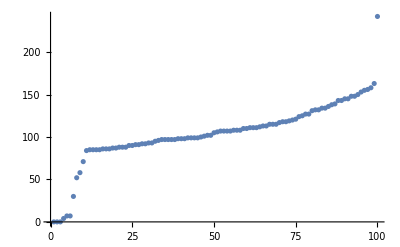

```mathematica
ds2[All,"runtime"]//Normal//Sort//ListPlot
```